```mathematica
Get["DV_Gradient/DV_GradientDefinitions.m"];
```

```mathematica
Get["TransportFunctions/XDataCreation.m"]
```

```mathematica
XDatam55p05Bins32=XDataCreation[{-0.055,0.005,0.},32]
```

{-0.055,-0.0530645,-0.051129,-0.0491935,-0.0472581,-0.0453226,-0.0433871,-0.0414516,-0.0395161,-0.0375806,-0.0356452,-0.0337097,-0.0317742,-0.0298387,-0.0279032,-0.0259677,-0.0240323,-0.0220968,-0.0201613,-0.0182258,-0.0162903,-0.0143548,-0.0124194,-0.0104839,-0.00854839,-0.0066129,-0.00467742,-0.00274194,-0.000806452,0.00112903,0.00306452,0.005}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
FitFuncMemoArithDVGrad[
{b_,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},{kDV_,LDV_},XList_,IntPrec_
]:=
FitFuncMemoArithDVGrad[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},{kDV,LDV},XList,IntPrec]=
Reverse[IntTableArithDVGrad[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},{kDV,LDV},XList,IntPrec]]
```

### bin selection and normalization

```mathematica
FitFuncBinNormArithDVGrad[bin_?NumericQ,{b_?NumericQ,alpha_,BRxB_,rRxB_,rD_,rF_,rA_},{xA_,yA_,xOff_,yOff_,y0_},{kDV_,LDV_},XList_,IntPrec_]:=FitFuncMemoArithDVGrad[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},{kDV,LDV},XList,IntPrec][[bin]]/Total[FitFuncMemoArithDVGrad[{b,alpha,BRxB,rRxB,rD,rF,rA},{xA,yA,xOff,yOff,y0},{kDV,LDV},XList,IntPrec]]
```

Data 90° no Filter

```mathematica
t0=AbsoluteTime[];
ILLData90noFilter=Table[{bin,FitFuncBinNormArithDVGrad[bin,{0.,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},{0.1,0.2},XDatam55p05Bins32,3]},{bin,1,Length[XDatam55p05Bins32]}];
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222532 and 0.000236912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126636 and 0.000122335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667707 and 0.0000264841 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401059 and 0.0401011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572254 and 0.0000597574 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856155 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123692 and 0.000521319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175312 and 0.000557132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242653 and 0.000679067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331423 and 0.000799909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449656 and 0.00111908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607585 and 0.00334789 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812354 and 0.00205923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06851 and 0.00341763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36877 and 0.0036124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70013 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03968 and 0.00663532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35851 and 0.00617982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63377 and 0.0055493 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.0060212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90326 and 0.00641663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75156 and 0.00542381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46043 and 0.00497589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46871 and 0.00295856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01395 and 0.00367092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956444 and 0.00209169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525028 and 0.00312971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200985 and 0.0171804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328126 and 0.000221848 for the integral and error estimates.

932.233101

### 932s

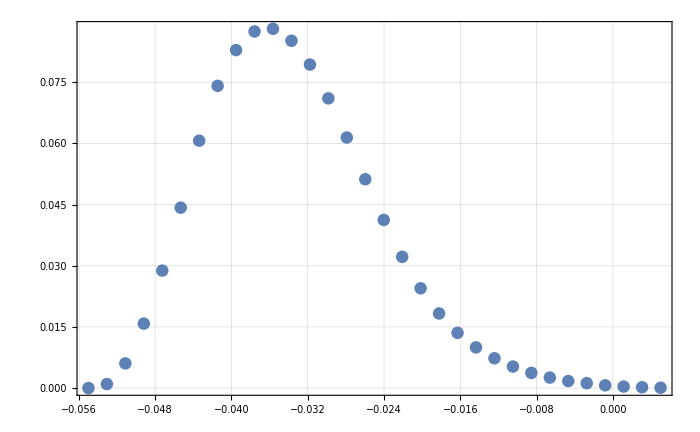

```mathematica
ListPlot[Transpose[{XDatam55p05Bins32,ILLData90noFilter[[All,2]]}]]
```

Fits

### dkDV fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dkDVFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArithDVGrad[bin,{b,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},{0.1+0.1*10^-4,0.2},XDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->8,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Wed 3 Jul 2019 14:52:06

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222527 and 0.000236904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066769 and 0.0000264843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126632 and 0.000122333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.040105 and 0.0401003 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856137 and 0.000240342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572242 and 0.0000597591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12369 and 0.000521311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175308 and 0.000557118 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242649 and 0.000679053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449649 and 0.00111906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331417 and 0.000799896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607575 and 0.00334785 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812343 and 0.00205923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.0685 and 0.00341765 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36876 and 0.00361237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70011 and 0.00302193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03966 and 0.00663532 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.3585 and 0.00617975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63376 and 0.00554929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90326 and 0.00641671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75157 and 0.00542391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46045 and 0.00497593 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01397 and 0.00367093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46873 and 0.00295859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956458 and 0.00209166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525036 and 0.00312975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200989 and 0.0171804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328135 and 0.000221859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222611 and 0.000237008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667959 and 0.0000264954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126682 and 0.000122382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401182 and 0.0401135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572442 and 0.0000597814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856423 and 0.000240438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12373 and 0.000521214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175362 and 0.000557268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242719 and 0.000679261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331508 and 0.000800126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449766 and 0.00111934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607726 and 0.00334883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812533 and 0.00205981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06873 and 0.00341863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36903 and 0.003613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.7004 and 0.00302249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03995 and 0.00663563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35875 and 0.00618007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63393 and 0.00554962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82748 and 0.0110009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92491 and 0.00602105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90306 and 0.00641619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75124 and 0.00542313 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46004 and 0.00497486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01355 and 0.00367029 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46836 and 0.00295792 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956181 and 0.00209131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.52486 and 0.00312898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200904 and 0.0171789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327956 and 0.000221731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222617 and 0.000237016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667979 and 0.0000264962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126686 and 0.000122386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401192 and 0.0401145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856445 and 0.000240445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572457 and 0.0000597831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123733 and 0.000521226 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175366 and 0.000557279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242725 and 0.000679277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331515 and 0.000800144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449775 and 0.00111936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607738 and 0.00334891 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812547 and 0.00205986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06875 and 0.0034187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36905 and 0.00361305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70042 and 0.00302253 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03997 and 0.00663565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35877 and 0.00618009 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63395 and 0.00554964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82749 and 0.0110008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9249 and 0.00602103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90304 and 0.00641615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75122 and 0.00542307 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46001 and 0.00497477 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01351 and 0.00367024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46833 and 0.00295786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95616 and 0.00209128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524846 and 0.00312892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200898 and 0.0171787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327942 and 0.000221722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222607 and 0.000237003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667946 and 0.0000264948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126679 and 0.00012238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401176 and 0.0401129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572432 and 0.0000597804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123728 and 0.000521206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085641 and 0.000240433 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175359 and 0.000557261 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242716 and 0.000679251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331504 and 0.000800115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449761 and 0.00111932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607719 and 0.00334879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812524 and 0.00205978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36901 and 0.00361297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06872 and 0.00341858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70039 and 0.00302247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03993 and 0.00663561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63393 and 0.0055496 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35873 and 0.00618005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82748 and 0.0110009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92491 and 0.00602106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75126 and 0.00542317 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90307 and 0.00641621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46006 and 0.00497491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01357 and 0.00367032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46838 and 0.00295795 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956194 and 0.00209133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524868 and 0.00312902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200909 and 0.0171789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327965 and 0.000221737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222542 and 0.000236923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126641 and 0.000122342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667738 and 0.0000264863 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401074 and 0.0401027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572278 and 0.0000597632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856189 and 0.000240359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123697 and 0.000521341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175318 and 0.000557145 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242662 and 0.000679091 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331433 and 0.000799938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44967 and 0.00111911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607603 and 0.00334803 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812377 and 0.00205933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06854 and 0.00341782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36881 and 0.00361248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70016 and 0.00302203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03971 and 0.00663537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35854 and 0.0061798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63379 and 0.00554935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82743 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92496 and 0.00602122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90323 and 0.00641662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75151 and 0.00542377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46038 and 0.00497573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0139 and 0.00367081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46866 and 0.00295847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956408 and 0.0020916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525004 and 0.00312961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200974 and 0.0171801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328103 and 0.000221836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222608 and 0.000237004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667949 and 0.000026495 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012668 and 0.000122381 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401177 and 0.040113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856413 and 0.000240435 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123728 and 0.000521208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572435 and 0.0000597806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.17536 and 0.000557263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242717 and 0.000679254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331505 and 0.000800118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449762 and 0.00111933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607721 and 0.0033488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812526 and 0.00205979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06872 and 0.00341859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36902 and 0.00361298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70039 and 0.00302247 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03994 and 0.00663562 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35874 and 0.00618005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63393 and 0.00554961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82748 and 0.0110009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92491 and 0.00602105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90306 and 0.00641621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75125 and 0.00542316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46006 and 0.0049749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46837 and 0.00295794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01356 and 0.00367032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956191 and 0.00209132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524866 and 0.00312901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200907 and 0.0171789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327962 and 0.000221736 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222452 and 0.000236811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126588 and 0.000122289 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066745 and 0.0000264744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400933 and 0.0400886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572064 and 0.0000597393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855882 and 0.000240257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123655 and 0.000521163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175261 and 0.000556985 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242586 and 0.000678868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331336 and 0.000799691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449544 and 0.00111881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607441 and 0.00334698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812174 and 0.00206102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06829 and 0.00341678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36852 and 0.0036118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69985 and 0.00302143 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0394 and 0.00663504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35827 and 0.00617946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63361 and 0.00554901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82736 and 0.0110017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90345 and 0.00641717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92503 and 0.00602144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75186 and 0.00541444 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46081 and 0.00497694 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01435 and 0.00367149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46905 and 0.00295919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956704 and 0.00209197 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525193 and 0.00313044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201064 and 0.0171818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328295 and 0.000221972 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.022261 and 0.000237007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126681 and 0.000122382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667957 and 0.0000264953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401181 and 0.0401134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057244 and 0.0000597813 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856421 and 0.000240437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123729 and 0.000521212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175361 and 0.000557267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242719 and 0.000679259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331507 and 0.000800124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449765 and 0.00111933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607725 and 0.00334882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812531 and 0.00205981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06873 and 0.00341862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36902 and 0.00361299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.7004 and 0.00302249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03994 and 0.00663563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35874 and 0.00618006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63393 and 0.00554962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82748 and 0.0110009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92491 and 0.00602105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90306 and 0.00641619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75125 and 0.00542313 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46004 and 0.00497487 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01355 and 0.0036703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46836 and 0.00295792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956183 and 0.00209131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524861 and 0.00312899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200905 and 0.0171789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327958 and 0.000221732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222483 and 0.00023685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066755 and 0.0000264785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126607 and 0.000122307 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400982 and 0.0400935 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855988 and 0.000240292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572138 and 0.0000597475 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123669 and 0.000521224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175281 and 0.00055704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242612 and 0.000678945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331369 and 0.000799776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449588 and 0.00111891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607497 and 0.00334734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812244 and 0.00205893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06838 and 0.00341714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36862 and 0.00361204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69996 and 0.00302164 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35837 and 0.00617958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03951 and 0.00663515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63367 and 0.00554913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82738 and 0.0110015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90337 and 0.00641698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92501 and 0.00602136 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75174 and 0.00541415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46066 and 0.00497652 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0142 and 0.00367126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46892 and 0.00295894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956601 and 0.00209184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525128 and 0.00313016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201033 and 0.0171812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328229 and 0.000221925 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222446 and 0.000236804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066743 and 0.0000264736 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126585 and 0.000122285 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400923 and 0.0400876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572049 and 0.0000597376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085586 and 0.00024025 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123652 and 0.00052115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175257 and 0.000556973 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242581 and 0.000678853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331329 and 0.000799674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449535 and 0.00111879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60743 and 0.00334691 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812159 and 0.00206097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06827 and 0.0034167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.3685 and 0.00361176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69983 and 0.00302139 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03939 and 0.00665506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35826 and 0.00617944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63359 and 0.00554898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82736 and 0.0110017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92504 and 0.00602146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90346 and 0.00641721 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75189 and 0.0054145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46084 and 0.00497703 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46908 and 0.00295924 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01439 and 0.00367154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956725 and 0.002092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525206 and 0.0031305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201071 and 0.0171819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328308 and 0.000221982 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222611 and 0.000237008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126682 and 0.000122382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667959 and 0.0000264954 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401182 and 0.0401135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572442 and 0.0000597814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856423 and 0.000240438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12373 and 0.000521214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175362 and 0.000557268 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242719 and 0.000679261 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331508 and 0.000800126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449766 and 0.00111934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607726 and 0.00334883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812533 and 0.00205981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06873 and 0.00341863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36903 and 0.003613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.7004 and 0.00302249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03995 and 0.00663563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35875 and 0.00618007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63393 and 0.00554962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82748 and 0.0110009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92491 and 0.00602105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90306 and 0.00641619 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75124 and 0.00542313 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46004 and 0.00497486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01355 and 0.00367029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46836 and 0.00295792 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956181 and 0.00209131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.52486 and 0.00312898 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200904 and 0.0171789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327956 and 0.000221731 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222474 and 0.000236839 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066752 and 0.0000264773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126601 and 0.000122302 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400968 and 0.0400921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855957 and 0.000240282 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572116 and 0.0000597451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123665 and 0.000521206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175275 and 0.000557024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242605 and 0.000678923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33136 and 0.000799751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449575 and 0.00111888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607481 and 0.00334724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812223 and 0.00205886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06835 and 0.00341703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36859 and 0.00361197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69993 and 0.00302158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03948 and 0.00663512 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35834 and 0.00617955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63365 and 0.00554909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82738 and 0.0110015 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92502 and 0.00602139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90339 and 0.00641704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75178 and 0.00541424 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46071 and 0.00497665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01424 and 0.00367133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46896 and 0.00295901 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956631 and 0.00209188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525147 and 0.00313024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201042 and 0.0171814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328248 and 0.000221939 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222544 and 0.000236926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667746 and 0.0000264866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126643 and 0.000122343 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401078 and 0.0401031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856197 and 0.000240362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572284 and 0.0000597638 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123698 and 0.000521346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.17532 and 0.000557149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242664 and 0.000679097 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331436 and 0.000799944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449673 and 0.00111912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607607 and 0.00334806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812382 and 0.00205935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06854 and 0.00341785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36881 and 0.0036125 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70017 and 0.00302205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03972 and 0.00663538 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35855 and 0.00617981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.6338 and 0.00554936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82743 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92496 and 0.00602121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90322 and 0.0064166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7515 and 0.00542374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46036 and 0.00497569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01388 and 0.00367079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46865 and 0.00295845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.9564 and 0.00209159 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524999 and 0.00312959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200971 and 0.0171801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328098 and 0.000221832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222526 and 0.000236903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667688 and 0.0000264842 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126632 and 0.000122333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401049 and 0.0401002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057224 and 0.000059759 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856135 and 0.000240341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12369 and 0.00052131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175308 and 0.000557117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242648 and 0.000679052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331416 and 0.000799894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449648 and 0.00111906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607574 and 0.00334784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812341 and 0.00205922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06849 and 0.00341764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36876 and 0.00361236 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70011 and 0.00302193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03966 and 0.00663531 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.3585 and 0.00617974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63376 and 0.00554929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75157 and 0.00542391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90326 and 0.00641671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46045 and 0.00497594 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01398 and 0.00367093 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46873 and 0.00295859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95646 and 0.00209166 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525037 and 0.00312976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20099 and 0.0171804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328137 and 0.00022186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222605 and 0.000237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667939 and 0.0000264946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126678 and 0.000122379 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401172 and 0.0401125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856403 and 0.000240431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572427 and 0.0000597798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123727 and 0.000521202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175358 and 0.000557257 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242714 and 0.000679246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331501 and 0.000800109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449758 and 0.00111932 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607715 and 0.00334876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812519 and 0.00205977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06871 and 0.00341856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36901 and 0.00361295 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70038 and 0.00302245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03992 and 0.00663561 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35873 and 0.00618004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63392 and 0.00554959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82748 and 0.0110009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92491 and 0.00602106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90307 and 0.00641623 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75127 and 0.00542318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46007 and 0.00497494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01358 and 0.00367034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46838 and 0.00295796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956201 and 0.00209134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524872 and 0.00312904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200911 and 0.017179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327969 and 0.000221741 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222579 and 0.000236969 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667857 and 0.0000264912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126663 and 0.000122364 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401132 and 0.0401085 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856315 and 0.000240402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572366 and 0.000059773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123715 and 0.000521415 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175342 and 0.000557211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242693 and 0.000679182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331474 and 0.000800039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449722 and 0.00111923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607669 and 0.00334846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812461 and 0.00205959 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06864 and 0.00341826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36893 and 0.00361276 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70029 and 0.00302228 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03984 and 0.00663551 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35865 and 0.00617995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63387 and 0.0055495 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82746 and 0.011001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92493 and 0.00602112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90313 and 0.00641639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75137 and 0.00542342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4602 and 0.00497529 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01371 and 0.00367053 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4685 and 0.00295817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956285 and 0.00209144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524926 and 0.00312927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200936 and 0.0171794 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328024 and 0.00022178 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222457 and 0.000236818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126591 and 0.000122292 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667466 and 0.0000264751 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400941 and 0.0400894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572076 and 0.0000597406 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855899 and 0.000240262 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123657 and 0.000521173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175264 and 0.000556994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24259 and 0.000678881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331341 and 0.000799705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449551 and 0.00111883 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60745 and 0.00334704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.0683 and 0.00341683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812185 and 0.00206105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36853 and 0.00361184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69987 and 0.00302147 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03942 and 0.00663506 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35829 and 0.00617948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63362 and 0.00554903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82736 and 0.0110016 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92503 and 0.00602143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90344 and 0.00641714 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75184 and 0.0054144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46079 and 0.00497688 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46903 and 0.00295915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01433 and 0.00367145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956687 and 0.00209195 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525183 and 0.0031304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201059 and 0.0171817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328284 and 0.000221965 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222442 and 0.000236799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667418 and 0.0000264731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126583 and 0.000122283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400918 and 0.0400871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855848 and 0.000240245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057204 and 0.0000597367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12365 and 0.000521143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175255 and 0.000556967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242578 and 0.000678844 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331325 and 0.000799664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44953 and 0.00111878 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607424 and 0.00334687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812151 and 0.00206095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06826 and 0.00341666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36849 and 0.00361173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69982 and 0.00302137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03938 and 0.00665504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35825 and 0.00617942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63359 and 0.00554897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82735 and 0.0110017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92504 and 0.00602147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90347 and 0.00641723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7519 and 0.00541453 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46086 and 0.00497708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0144 and 0.00367157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4691 and 0.00295927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956736 and 0.00209201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525214 and 0.00313053 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201074 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328316 and 0.000221987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.02225 and 0.00023687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667603 and 0.0000264807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126617 and 0.000122317 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401008 and 0.0400961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856045 and 0.000240311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572177 and 0.0000597519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123677 and 0.000521257 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175291 and 0.00055707 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242626 and 0.000678986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331388 and 0.000799822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449611 and 0.00111897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607527 and 0.00334754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812281 and 0.00205904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06842 and 0.00341733 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36867 and 0.00361216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70001 and 0.00302175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03956 and 0.00663522 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35842 and 0.00617964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.6337 and 0.00554919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8274 and 0.0110014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.925 and 0.00602132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90333 and 0.00641688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75167 and 0.005414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46058 and 0.0049763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01411 and 0.00367113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46885 and 0.0029588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956547 and 0.00209177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525093 and 0.00313 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201016 and 0.0171809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328193 and 0.0002219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222551 and 0.000236934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667767 and 0.0000264875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126647 and 0.000122347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401088 and 0.0401041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.05723 and 0.0000597656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085622 and 0.00024037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123701 and 0.000521359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175324 and 0.000557161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242669 and 0.000679113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331443 and 0.000799962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449683 and 0.00111914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607619 and 0.00334814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812398 and 0.0020594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06856 and 0.00341793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36884 and 0.00361255 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70019 and 0.00302209 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03974 and 0.00663541 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35857 and 0.00617984 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63381 and 0.00554939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82744 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92495 and 0.00602119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.9032 and 0.00641656 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75148 and 0.00542368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46033 and 0.0049756 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01385 and 0.00367074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46862 and 0.00295839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956378 and 0.00209156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524985 and 0.00312953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200965 and 0.01718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328084 and 0.000221822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222494 and 0.000236863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667585 and 0.00002648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126613 and 0.000122314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400999 and 0.0400952 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572164 and 0.0000597504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856025 and 0.000240305 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123675 and 0.000521246 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175288 and 0.00055706 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242621 and 0.000678972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331381 and 0.000799806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449603 and 0.00111895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607517 and 0.00334747 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812268 and 0.002059 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06841 and 0.00341727 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36865 and 0.00361212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69999 and 0.00302171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03955 and 0.00663519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.3584 and 0.00617962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63369 and 0.00554917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82739 and 0.0110014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.925 and 0.00602134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90334 and 0.00641691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7517 and 0.00541405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46061 and 0.00497638 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01414 and 0.00367117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46887 and 0.00295885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956565 and 0.0020918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525105 and 0.00313006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201022 and 0.017181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328205 and 0.000221908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222545 and 0.000236927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667749 and 0.0000264867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126643 and 0.000122344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401079 and 0.0401032 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572286 and 0.0000597641 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.08562 and 0.000240363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123699 and 0.000521348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.17532 and 0.000557151 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242664 and 0.000679099 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331437 and 0.000799947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449675 and 0.00111912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607609 and 0.00334807 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812385 and 0.00205936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06855 and 0.00341786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36882 and 0.00361251 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70017 and 0.00302206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03972 and 0.00663539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35855 and 0.00617982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.6338 and 0.00554937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82743 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92496 and 0.00602121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90322 and 0.00641659 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7515 and 0.00542373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46036 and 0.00497568 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01388 and 0.00367079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46865 and 0.00295844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956396 and 0.00209158 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524997 and 0.00312958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20097 and 0.0171801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328096 and 0.000221831 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.022251 and 0.000236883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126623 and 0.000122323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667635 and 0.0000264821 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401024 and 0.0400977 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856079 and 0.000240323 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572202 and 0.0000597546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123682 and 0.000521278 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175298 and 0.000557088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242635 and 0.000679011 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331399 and 0.00079985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449625 and 0.001119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607545 and 0.00334766 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.3687 and 0.00361224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812304 and 0.00205911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06845 and 0.00341745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70005 and 0.00302182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35845 and 0.00617968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0396 and 0.00663525 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63373 and 0.00554923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8274 and 0.0110014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92499 and 0.0060213 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.9033 and 0.00641681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75164 and 0.00541391 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46053 and 0.00497616 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4688 and 0.00295872 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01406 and 0.00367105 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956513 and 0.00209173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201006 and 0.0171807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328171 and 0.000221884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222442 and 0.000236799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667418 and 0.0000264731 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126583 and 0.000122283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400917 and 0.040087 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057204 and 0.0000597366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855847 and 0.000240245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12365 and 0.000521143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175254 and 0.000556967 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242578 and 0.000678843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331325 and 0.000799664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44953 and 0.00111878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607423 and 0.00334686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812151 and 0.00206095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06826 and 0.00341666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36849 and 0.00361173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69981 and 0.00302137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03937 and 0.00665504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35824 and 0.00617942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63358 and 0.00554897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82735 and 0.0110017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92504 and 0.00602147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90347 and 0.00641723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7519 and 0.00541453 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46086 and 0.00497708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01441 and 0.00367157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4691 and 0.00295927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956737 and 0.00209202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525214 and 0.00313054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201075 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328316 and 0.000221987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222444 and 0.000236802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126584 and 0.000122285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667425 and 0.0000264734 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400921 and 0.0400874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855855 and 0.000240248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572045 and 0.0000597372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123651 and 0.000521147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175256 and 0.000556971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24258 and 0.000678849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331327 and 0.00079967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449533 and 0.00111878 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607427 and 0.00334689 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812156 and 0.00206096 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06827 and 0.00341668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36849 and 0.00361174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69982 and 0.00302138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03938 and 0.00665505 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35825 and 0.00617943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63359 and 0.00554898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82735 and 0.0110017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92504 and 0.00602146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90347 and 0.00641722 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75189 and 0.00541451 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46085 and 0.00497705 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46909 and 0.00295925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01439 and 0.00367155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95673 and 0.00209201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.52521 and 0.00313052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201072 and 0.0171819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328312 and 0.000221984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222566 and 0.000236953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667817 and 0.0000264895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126656 and 0.000122356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401113 and 0.0401066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856273 and 0.000240388 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572337 and 0.0000597697 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123709 and 0.00052139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175334 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242682 and 0.000679152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33146 and 0.000800005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449704 and 0.00111919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607647 and 0.00334832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812433 and 0.00205951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06861 and 0.00341811 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36889 and 0.00361267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70025 and 0.0030222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03979 and 0.00663546 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35862 and 0.0061799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63384 and 0.00554945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82745 and 0.0110011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92494 and 0.00602116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90317 and 0.00641646 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75141 and 0.00542354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46026 and 0.00497546 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01377 and 0.00367063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46855 and 0.00295827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956326 and 0.00209149 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524952 and 0.00312939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200949 and 0.0171797 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032805 and 0.000221798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222536 and 0.000236915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667719 and 0.0000264855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126638 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401065 and 0.0401018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572263 and 0.0000597615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856168 and 0.000240353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331427 and 0.000799921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607592 and 0.00334796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812363 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75153 and 0.00542382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956428 and 0.00209162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525017 and 0.00312967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20098 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328116 and 0.000221845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222556 and 0.000236941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.0000264882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401097 and 0.040105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572312 and 0.000059767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856238 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123704 and 0.00052137 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175327 and 0.000557171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242674 and 0.000679126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331449 and 0.000799977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44969 and 0.00111916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607629 and 0.0033482 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.81241 and 0.00205943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06858 and 0.00341799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36885 and 0.00361259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70021 and 0.00302213 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03976 and 0.00663543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35859 and 0.00617986 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63382 and 0.00554941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82744 and 0.0110011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90319 and 0.00641653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92495 and 0.00602118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75145 and 0.00542363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46031 and 0.00497553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01382 and 0.0036707 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4686 and 0.00295835 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95636 and 0.00209154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524974 and 0.00312948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200959 and 0.0171799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328072 and 0.000221814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.02225 and 0.000236871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126617 and 0.000122318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667605 and 0.0000264808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401009 and 0.0400962 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572179 and 0.0000597521 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856047 and 0.000240312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123678 and 0.000521259 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175292 and 0.000557071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242627 and 0.000678988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331388 and 0.000799824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449612 and 0.00111897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607528 and 0.00334754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812283 and 0.00205905 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06842 and 0.00341734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36867 and 0.00361217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70002 and 0.00302176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03957 and 0.00663522 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35842 and 0.00617965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63371 and 0.00554919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8274 and 0.0110014 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.925 and 0.00602132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90333 and 0.00641687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75167 and 0.005414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46058 and 0.00497629 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01411 and 0.00367113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.0029588 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956544 and 0.00209177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525091 and 0.00313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201016 and 0.0171809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328192 and 0.000221899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222519 and 0.000236894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667665 and 0.0000264833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126628 and 0.000122328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401038 and 0.0400991 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085611 and 0.000240333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572223 and 0.0000597571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123686 and 0.000521296 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175303 and 0.000557104 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242642 and 0.000679034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331408 and 0.000799875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449638 and 0.00111903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607562 and 0.00334776 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812325 and 0.00205917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06847 and 0.00341756 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36873 and 0.00361231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70008 and 0.00302188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03963 and 0.00663529 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35847 and 0.00617972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63374 and 0.00554927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82741 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92498 and 0.00602127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90328 and 0.00641676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7516 and 0.00541382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46049 and 0.00497604 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01401 and 0.00367099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46876 and 0.00295865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956483 and 0.00209169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525052 and 0.00312983 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200997 and 0.0171805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328152 and 0.000221871 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222536 and 0.000236915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667719 and 0.0000264855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126638 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401065 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856168 and 0.000240353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572263 and 0.0000597615 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331427 and 0.000799921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607592 and 0.00334796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812363 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75153 and 0.00542382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295851 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956428 and 0.00209162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525017 and 0.00312967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20098 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328116 and 0.000221845 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222586 and 0.000236978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126667 and 0.000122368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066788 and 0.0000264921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401144 and 0.0401097 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572384 and 0.0000597749 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085634 and 0.00024041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123718 and 0.000521165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175346 and 0.000557224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242699 and 0.000679201 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331482 and 0.000800059 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449732 and 0.00111926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607682 and 0.00334855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812477 and 0.00205964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36895 and 0.00361281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06866 and 0.00341834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03986 and 0.00663554 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35867 and 0.00617997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63388 and 0.00554952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82746 and 0.011001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92493 and 0.00602111 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90312 and 0.00641634 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75134 and 0.00542335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46016 and 0.00497519 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01367 and 0.00367048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46847 and 0.00295811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956261 and 0.00209141 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524911 and 0.0031292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200929 and 0.0171793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328008 and 0.000221768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222558 and 0.000236942 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667789 and 0.0000264884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126651 and 0.000122351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401099 and 0.0401052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572316 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856243 and 0.000240378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123705 and 0.000521373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175328 and 0.000557174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242675 and 0.00067913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331451 and 0.000799981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449692 and 0.00111916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607631 and 0.00334822 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812413 and 0.00205945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06858 and 0.00341801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36886 and 0.0036126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70022 and 0.00302214 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03976 and 0.00663543 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35859 and 0.00617987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63383 and 0.00554941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82744 and 0.0110011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92495 and 0.00602118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90319 and 0.00641652 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75145 and 0.00542362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4603 and 0.00497551 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01382 and 0.00367069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46859 and 0.00295834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956355 and 0.00209153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524971 and 0.00312947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200958 and 0.0171798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328069 and 0.000221811 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222555 and 0.000236939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066778 and 0.000026488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126649 and 0.00012235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401095 and 0.0401048 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572309 and 0.0000597667 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856234 and 0.000240374 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123703 and 0.000521367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175326 and 0.000557169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242673 and 0.000679123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331448 and 0.000799974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449688 and 0.00111915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607626 and 0.00334818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06857 and 0.00341798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812407 and 0.00205943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36885 and 0.00361258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70021 and 0.00302212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03975 and 0.00663542 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35858 and 0.00617985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63382 and 0.0055494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82744 and 0.0110011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92495 and 0.00602118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90319 and 0.00641653 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75146 and 0.00542364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46031 and 0.00497555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4686 and 0.00295836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01383 and 0.00367071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956364 and 0.00209154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524977 and 0.00312949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200961 and 0.0171799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328075 and 0.000221816 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222541 and 0.000236922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667736 and 0.0000264862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126641 and 0.000122342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401073 and 0.0401026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572277 and 0.000059763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856187 and 0.000240359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123697 and 0.00052134 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175318 and 0.000557144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242661 and 0.000679089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331433 and 0.000799936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449669 and 0.00111911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607602 and 0.00334802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812376 and 0.00205933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06854 and 0.00341782 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.3688 and 0.00361248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70016 and 0.00302203 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35854 and 0.0061798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03971 and 0.00663537 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63379 and 0.00554935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82743 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92496 and 0.00602122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90323 and 0.00641662 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75151 and 0.00542377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46038 and 0.00497573 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46866 and 0.00295847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0139 and 0.00367082 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95641 and 0.0020916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525005 and 0.00312962 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200974 and 0.0171801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328104 and 0.000221837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222516 and 0.000236891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126626 and 0.000122327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667655 and 0.0000264829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401033 and 0.0400986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.08561 and 0.00024033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572216 and 0.0000597563 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123685 and 0.00052129 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175302 and 0.000557099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24264 and 0.000679027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331405 and 0.000799867 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449634 and 0.00111902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607556 and 0.00334773 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812318 and 0.00205915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06847 and 0.00341752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36872 and 0.00361229 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70007 and 0.00302186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03962 and 0.00663528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35847 and 0.00617971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63374 and 0.00554925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82741 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92498 and 0.00602128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90329 and 0.00641678 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75161 and 0.00541385 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4605 and 0.00497608 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01403 and 0.00367101 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46877 and 0.00295867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956493 and 0.00209171 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525059 and 0.00312985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328158 and 0.000221875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222538 and 0.000236918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667725 and 0.0000264857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126639 and 0.00012234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401068 and 0.0401021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856175 and 0.000240355 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572268 and 0.0000597621 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123695 and 0.000521333 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175315 and 0.000557138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242658 and 0.000679081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331429 and 0.000799927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449664 and 0.0011191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607596 and 0.00334798 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812368 and 0.00205931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06853 and 0.00341778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361245 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70015 and 0.00302201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0397 and 0.00663536 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35853 and 0.00617979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82743 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92496 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641664 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75153 and 0.0054238 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4604 and 0.00497578 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46868 and 0.0029585 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01392 and 0.00367084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956421 and 0.00209161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525013 and 0.00312965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200978 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328112 and 0.000221842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222536 and 0.000236916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126638 and 0.000122339 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066772 and 0.0000264855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401065 and 0.0401018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856169 and 0.000240353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572265 and 0.0000597617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.00052133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242657 and 0.000679077 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331427 and 0.000799922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449662 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607593 and 0.00334796 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341776 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812364 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361244 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.003022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35853 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75153 and 0.00542382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4604 and 0.0049758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295851 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956426 and 0.00209162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525016 and 0.00312967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20098 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328115 and 0.000221844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222517 and 0.000236893 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066766 and 0.0000264831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126627 and 0.000122328 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401036 and 0.0400989 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057222 and 0.0000597567 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856106 and 0.000240332 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123686 and 0.000521293 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175303 and 0.000557102 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242641 and 0.000679031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449636 and 0.00111903 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331407 and 0.000799871 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607559 and 0.00334775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812322 and 0.00205917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36873 and 0.0036123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06847 and 0.00341754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70008 and 0.00302187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03963 and 0.00663528 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35847 and 0.00617971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63374 and 0.00554926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82741 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92498 and 0.00602128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90329 and 0.00641677 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75161 and 0.00541384 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46049 and 0.00497606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46877 and 0.00295866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01402 and 0.003671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956488 and 0.0020917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525055 and 0.00312984 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200998 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328155 and 0.000221873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667718 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126638 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856167 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572263 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679075 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.00079992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641665 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497581 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956429 and 0.00209162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312967 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20098 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222522 and 0.000236898 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667675 and 0.0000264837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012663 and 0.00012233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401043 and 0.0400996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572231 and 0.0000597579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856121 and 0.000240337 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123688 and 0.000521302 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175305 and 0.00055711 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242645 and 0.000679042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331412 and 0.000799883 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449642 and 0.00111904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607567 and 0.0033478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812332 and 0.0020592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06848 and 0.00341759 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36874 and 0.00361233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70009 and 0.0030219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03964 and 0.0066353 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35848 and 0.00617973 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63375 and 0.00554928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82741 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92498 and 0.00602127 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90327 and 0.00641674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75159 and 0.00542395 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46047 and 0.004976 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.014 and 0.00367096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46875 and 0.00295863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956473 and 0.00209168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525046 and 0.0031298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200994 and 0.0171805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328145 and 0.000221866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.016209 and 0.000161273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0047397 and 0.0000186094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00911273 and 0.0000706655 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0306331 and 0.03063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0428288 and 0.0000440168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0650328 and 0.000173065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0952176 and 0.000421427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.136807 and 0.000454636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.192119 and 0.000543103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.26584 and 0.000579533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.364889 and 0.000972961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.499004 and 0.00253933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.675707 and 0.00182515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.901749 and 0.00398705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.49098 and 0.00262846 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.17491 and 0.00307555 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.18027 and 0.00598919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.83228 and 0.00602467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78095 and 0.0117575 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.50776 and 0.0082875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.97484 and 0.00592132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.05296 and 0.00669764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.98838 and 0.00627689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.75404 and 0.00598461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.15544 and 0.00407908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.73372 and 0.00222988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.32146 and 0.00405552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.652134 and 0.00364824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.262432 and 0.0178151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0457069 and 0.000307698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.016209 and 0.000161273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0047397 and 0.0000186094 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00911273 and 0.0000706655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0306331 and 0.03063 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0650328 and 0.000173065 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0428288 and 0.0000440168 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0952176 and 0.000421427 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.136807 and 0.000454636 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.192119 and 0.000543103 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.26584 and 0.000579533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.364889 and 0.000972961 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.499004 and 0.00253933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.675707 and 0.00182515 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.901749 and 0.00398705 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.17491 and 0.00307555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.49098 and 0.00262846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.83228 and 0.00602467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.50776 and 0.0082875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.18027 and 0.00598919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78095 and 0.0117575 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.97484 and 0.00592132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.05296 and 0.00669764 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.98838 and 0.00627689 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.75404 and 0.00598461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.32146 and 0.00405552 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.73372 and 0.00222988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.15544 and 0.00407908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.652134 and 0.00364824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.262432 and 0.0178151 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0457069 and 0.000307698 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0169154 and 0.000170017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.00496613 and 0.0000195008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00953243 and 0.0000737161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0317401 and 0.0317368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0674719 and 0.000170194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.044511 and 0.0000457587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0985473 and 0.000436019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.141302 and 0.000468439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.198032 and 0.00055789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.27351 and 0.000599378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.374779 and 0.00100018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.51165 and 0.00263873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.691553 and 0.00191758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.921315 and 0.00414089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.19757 and 0.00311055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.51526 and 0.00270035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.85649 and 0.00609565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.20118 and 0.0060285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.52292 and 0.00562463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78665 and 0.0116661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.96833 and 0.00609499 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.03568 and 0.00627231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.95696 and 0.00560494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.71979 and 0.00578794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.28548 and 0.00406116 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.70237 and 0.0020405 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.13216 and 0.00400712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.637291 and 0.00359095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.255301 and 0.0177142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0442 and 0.000297211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0169154 and 0.000170017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.00496613 and 0.0000195008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00953243 and 0.0000737161 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0317401 and 0.0317368 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.044511 and 0.0000457587 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0674719 and 0.000170194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0985473 and 0.000436019 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.141302 and 0.000468439 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.198032 and 0.00055789 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.27351 and 0.000599378 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.374779 and 0.00100018 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.51165 and 0.00263873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.691553 and 0.00191758 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.921315 and 0.00414089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.19757 and 0.00311055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.51526 and 0.00270035 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.85649 and 0.00609565 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.20118 and 0.0060285 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.52292 and 0.00562463 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78665 and 0.0116661 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.03568 and 0.00627231 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.96833 and 0.00609499 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.95696 and 0.00560494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.71979 and 0.00578794 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.28548 and 0.00406116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.70237 and 0.0020405 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.13216 and 0.00400712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.637291 and 0.00359095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.255301 and 0.0177142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0442 and 0.000297211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222535 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667717 and 0.0000264854 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126637 and 0.000122338 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856166 and 0.000240352 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.000521328 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572262 and 0.0000597614 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175314 and 0.000557133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242656 and 0.000679074 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331426 and 0.000799919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449661 and 0.00111909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607591 and 0.00334795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812362 and 0.00205929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06852 and 0.00341775 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70014 and 0.00302199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03969 and 0.00663535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35852 and 0.00617978 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63378 and 0.00554933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110012 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90324 and 0.00641666 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497582 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01393 and 0.00367086 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46869 and 0.00295852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95643 and 0.00209163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525018 and 0.00312968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328117 and 0.000221846 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222531 and 0.000236909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667704 and 0.0000264849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126635 and 0.000122336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401057 and 0.040101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856152 and 0.000240347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572252 and 0.0000597603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123692 and 0.00052132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175311 and 0.000557126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242653 and 0.000679064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331422 and 0.000799908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449655 and 0.00111907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607583 and 0.0033479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812352 and 0.00205926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06851 and 0.0034177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36877 and 0.0036124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70012 and 0.00302196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03967 and 0.00663533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35851 and 0.00617976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63377 and 0.00554931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90325 and 0.00641668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75155 and 0.00542387 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46043 and 0.00497587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01395 and 0.00367089 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46871 and 0.00295855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956443 and 0.00209164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525027 and 0.00312971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200985 and 0.0171803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328126 and 0.000221852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222531 and 0.000236909 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667704 and 0.0000264849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126635 and 0.000122336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401057 and 0.040101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572252 and 0.0000597603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856152 and 0.000240347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123692 and 0.00052132 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175311 and 0.000557126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242653 and 0.000679064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331422 and 0.000799908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449655 and 0.00111907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607583 and 0.0033479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812352 and 0.00205926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06851 and 0.0034177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36877 and 0.0036124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70012 and 0.00302196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03967 and 0.00663533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35851 and 0.00617976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63377 and 0.00554931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90325 and 0.00641668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75155 and 0.00542387 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46043 and 0.00497587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46871 and 0.00295855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01395 and 0.00367089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956443 and 0.00209164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525027 and 0.00312971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200985 and 0.0171803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328126 and 0.000221852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222531 and 0.00023691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667704 and 0.0000264849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126635 and 0.000122336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401057 and 0.040101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856152 and 0.000240347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572253 and 0.0000597603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123692 and 0.00052132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175311 and 0.000557126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242653 and 0.000679064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331422 and 0.000799908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449655 and 0.00111907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607584 and 0.00334791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812353 and 0.00205926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06851 and 0.0034177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36877 and 0.0036124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70012 and 0.00302196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03967 and 0.00663533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35851 and 0.00617976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63377 and 0.00554931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90325 and 0.00641668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75155 and 0.00542386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46043 and 0.00497587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46871 and 0.00295855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01395 and 0.00367089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956443 and 0.00209164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525027 and 0.00312971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200985 and 0.0171803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328126 and 0.000221852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222531 and 0.00023691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667704 and 0.0000264849 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126635 and 0.000122336 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401057 and 0.040101 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572253 and 0.0000597603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856152 and 0.000240347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123692 and 0.00052132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175311 and 0.000557126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242653 and 0.000679064 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331422 and 0.000799908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449655 and 0.00111907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607584 and 0.00334791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812353 and 0.00205926 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06851 and 0.0034177 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36877 and 0.0036124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70012 and 0.00302196 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03967 and 0.00663533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35851 and 0.00617976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63377 and 0.00554931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82742 and 0.0110013 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92497 and 0.00602124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90325 and 0.00641668 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75155 and 0.00542386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46043 and 0.00497587 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46871 and 0.00295855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01395 and 0.00367089 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956443 and 0.00209164 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525027 and 0.00312971 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200985 and 0.0171803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328126 and 0.000221852 for the integral and error estimates.

44952.227974

### took 44952s or 12.5h

```mathematica
dkDVFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 2.28438×10^-7 | 4.701×10^-7 | 0.485935 | 0.630431

```mathematica
dkDVFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

0.00228438

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
dLDVFit=Reap[NonlinearModelFit[
ILLData90noFilter,
{
FitFuncBinNormArithDVGrad[bin,{b,Pi/2,0.2,1./2,1./2,1.,1/2.},{0.01,0.035,0.,0.,0.},{0.1,0.2+0.2*10^-4},XDatam55p05Bins32,3],
-0.002<b<0.002
},
{{b,0.0001}},bin,MaxIterations->8,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Thu 4 Jul 2019 03:21:19

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222549 and 0.000236928 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667756 and 0.0000264869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126645 and 0.000122345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.040109 and 0.0401043 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572299 and 0.0000597651 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856222 and 0.000240366 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123702 and 0.000521363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175326 and 0.000557174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242673 and 0.000679121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33145 and 0.000799976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449694 and 0.00111917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607636 and 0.00334819 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.0686 and 0.00341799 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812424 and 0.00205943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36889 and 0.00361273 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70028 and 0.00302223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03986 and 0.00663598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35873 and 0.00618036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63402 and 0.00554985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92527 and 0.00602186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90355 and 0.00641735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75185 and 0.00542445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4607 and 0.00497643 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01418 and 0.00367129 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46887 and 0.00295888 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956553 and 0.00209187 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525089 and 0.00313007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201009 and 0.0171821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328168 and 0.000221881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222633 and 0.000237032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126695 and 0.000122394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668026 and 0.000026498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401222 and 0.0401175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856509 and 0.000240462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572499 and 0.0000597874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123742 and 0.000521266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175379 and 0.000557324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242743 and 0.000679329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331541 and 0.000800206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449811 and 0.00111945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607787 and 0.00334917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812614 and 0.00206002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36916 and 0.00361336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06884 and 0.00341897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70057 and 0.00302279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04015 and 0.00663629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35898 and 0.00618068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.6342 and 0.00555017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82776 and 0.011002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9252 and 0.00602165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90335 and 0.00641683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75152 and 0.00542367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46029 and 0.00497536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01375 and 0.00367066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46851 and 0.00295821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956277 and 0.00209152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524912 and 0.00312929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200925 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327989 and 0.000221754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222639 and 0.000237039 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126698 and 0.000122398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668046 and 0.0000264988 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401232 and 0.0401185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572514 and 0.0000597891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856531 and 0.000240469 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123745 and 0.000521278 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175383 and 0.000557335 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242749 and 0.000679345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331548 and 0.000800224 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44982 and 0.00111947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607799 and 0.00334924 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812629 and 0.00206006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06885 and 0.00341904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36918 and 0.00361341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70059 and 0.00302284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04017 and 0.00663632 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.359 and 0.00618071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63421 and 0.0055502 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82777 and 0.0110019 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92519 and 0.00602163 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90333 and 0.00641679 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75149 and 0.00542361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46026 and 0.00497527 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46848 and 0.00295816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01372 and 0.00367061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956255 and 0.00209149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524899 and 0.00312923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200918 and 0.0171805 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327975 and 0.000221744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222629 and 0.000237027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668013 and 0.0000264975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126692 and 0.000122392 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401216 and 0.0401169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572489 and 0.0000597863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856495 and 0.000240457 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12374 and 0.000521258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175377 and 0.000557316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24274 and 0.000679319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331537 and 0.000800195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449806 and 0.00111944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60778 and 0.00334912 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812605 and 0.00205999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06882 and 0.00341892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36915 and 0.00361333 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70056 and 0.00302277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04014 and 0.00663628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35897 and 0.00618067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63419 and 0.00555016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82776 and 0.011002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9252 and 0.00602166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90336 and 0.00641686 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75153 and 0.00542371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46031 and 0.00497541 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01377 and 0.00367069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46852 and 0.00295824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95629 and 0.00209154 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524921 and 0.00312933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200929 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327998 and 0.00022176 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222564 and 0.000236946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667805 and 0.0000264889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126654 and 0.000122354 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401114 and 0.0401067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572335 and 0.0000597691 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856274 and 0.000240383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123709 and 0.000521393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175336 and 0.000557201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242686 and 0.000679159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331466 and 0.000800017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449715 and 0.00111922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607663 and 0.00334836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812458 and 0.00205954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06865 and 0.00341817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36894 and 0.00361284 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70033 and 0.00302234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03991 and 0.00663604 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35878 and 0.00618042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63406 and 0.00554991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92525 and 0.00602182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90352 and 0.00641726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75179 and 0.00542431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46062 and 0.00497622 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0141 and 0.00367118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46881 and 0.00295876 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956503 and 0.00209181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525057 and 0.00312993 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200994 and 0.0171818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328136 and 0.000221858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.022263 and 0.000237028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668016 and 0.0000264976 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126693 and 0.000122393 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401217 and 0.040117 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572492 and 0.0000597866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856499 and 0.000240459 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123741 and 0.00052126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175378 and 0.000557318 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242741 and 0.000679322 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331538 and 0.000800198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449807 and 0.00111944 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607782 and 0.00334913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06883 and 0.00341894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812607 and 0.00206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36915 and 0.00361334 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70056 and 0.00302277 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04014 and 0.00663628 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35897 and 0.00618067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63419 and 0.00555016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82776 and 0.011002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90335 and 0.00641685 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9252 and 0.00602166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75153 and 0.0054237 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4603 and 0.00497539 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46852 and 0.00295823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01376 and 0.00367068 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956286 and 0.00209153 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524918 and 0.00312932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200928 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327995 and 0.000221758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222474 and 0.000236835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667517 and 0.0000264771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126601 and 0.000122301 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400973 and 0.0400926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572121 and 0.0000597453 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855968 and 0.000240281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123667 and 0.000521215 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175278 and 0.00055704 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242611 and 0.000678936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331369 and 0.000799771 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449589 and 0.00111892 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607502 and 0.00334732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812255 and 0.00206122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.0684 and 0.00341712 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36866 and 0.00361216 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70002 and 0.00302174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03961 and 0.0066357 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35851 and 0.00618008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63387 and 0.00554956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82764 and 0.0110028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92533 and 0.00602204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90374 and 0.00641781 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75214 and 0.00541498 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46106 and 0.00497744 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4692 and 0.00295948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01456 and 0.00367186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956799 and 0.00209218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525246 and 0.00313076 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201085 and 0.0171835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328328 and 0.000221994 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222632 and 0.000237031 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668023 and 0.0000264979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126694 and 0.000122394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401221 and 0.0401174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572498 and 0.0000597872 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856507 and 0.000240461 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123742 and 0.000521264 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175379 and 0.000557322 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242743 and 0.000679327 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33154 and 0.000800204 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44981 and 0.00111945 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607786 and 0.00334916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812613 and 0.00206001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06883 and 0.00341896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36916 and 0.00361335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70057 and 0.00302279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04015 and 0.00663629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35898 and 0.00618068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.6342 and 0.00555017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82776 and 0.011002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9252 and 0.00602165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90335 and 0.00641683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75152 and 0.00542368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46029 and 0.00497536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01375 and 0.00367067 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46851 and 0.00295822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956279 and 0.00209152 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524914 and 0.0031293 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200925 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032799 and 0.000221755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222505 and 0.000236874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667616 and 0.0000264812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126619 and 0.00012232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401022 and 0.0400975 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856073 and 0.000240316 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572195 and 0.0000597535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123682 and 0.000521277 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175298 and 0.000557096 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242637 and 0.000679013 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331403 and 0.000799856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449633 and 0.00111902 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607558 and 0.00334768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06848 and 0.00341748 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812325 and 0.00205913 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36875 and 0.0036124 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70013 and 0.00302194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03971 and 0.00663582 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.3586 and 0.0061802 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63393 and 0.00554968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82767 and 0.0110026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9253 and 0.00602197 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90366 and 0.00641762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75201 and 0.0054147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46091 and 0.00497702 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46907 and 0.00295923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0144 and 0.00367162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956697 and 0.00209205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.52518 and 0.00313047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201053 and 0.0171829 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328261 and 0.000221947 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222468 and 0.000236827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667496 and 0.0000264762 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126597 and 0.000122298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400963 and 0.0400916 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572106 and 0.0000597436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855946 and 0.000240274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123664 and 0.000521202 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175274 and 0.000557029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242605 and 0.000678921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331362 and 0.000799754 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44958 and 0.0011189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607491 and 0.00334724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.81224 and 0.00206118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06838 and 0.00341704 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36864 and 0.00361212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.7 and 0.00302169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03959 and 0.00665572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35849 and 0.00618006 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63386 and 0.00554954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82764 and 0.0110028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92533 and 0.00602206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90375 and 0.00641785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75216 and 0.00541504 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46109 and 0.00497753 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01459 and 0.00367191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46923 and 0.00295953 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95682 and 0.00209221 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525259 and 0.00313081 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201091 and 0.0171836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328341 and 0.000222004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222633 and 0.000237032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668026 and 0.000026498 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126695 and 0.000122394 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401222 and 0.0401175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856509 and 0.000240462 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572499 and 0.0000597874 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123742 and 0.000521266 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175379 and 0.000557324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242743 and 0.000679329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331541 and 0.000800206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449811 and 0.00111945 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607787 and 0.00334917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812614 and 0.00206002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06884 and 0.00341897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36916 and 0.00361336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70057 and 0.00302279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04015 and 0.00663629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35898 and 0.00618068 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.6342 and 0.00555017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82776 and 0.011002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9252 and 0.00602165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90335 and 0.00641683 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75152 and 0.00542367 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46029 and 0.00497536 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01375 and 0.00367066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46851 and 0.00295821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956277 and 0.00209152 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524912 and 0.00312929 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200925 and 0.0171806 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0327989 and 0.000221754 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222496 and 0.000236862 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667587 and 0.00002648 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126614 and 0.000122314 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401008 and 0.0400961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572173 and 0.0000597511 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856042 and 0.000240306 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123677 and 0.000521258 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175292 and 0.00055708 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242629 and 0.000678991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331393 and 0.000799831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44962 and 0.00111899 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607542 and 0.00334757 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06846 and 0.00341737 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812304 and 0.00205907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36873 and 0.00361233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.7001 and 0.00302188 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03968 and 0.00663578 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35858 and 0.00618016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63391 and 0.00554965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82766 and 0.0110026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90368 and 0.00641768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92531 and 0.00602199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75205 and 0.00541478 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46095 and 0.00497714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46911 and 0.00295931 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01444 and 0.00367169 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956727 and 0.00209209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525199 and 0.00313055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201062 and 0.0171831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328281 and 0.000221961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222566 and 0.000236949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667813 and 0.0000264892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126655 and 0.000122356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401118 and 0.0401071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856282 and 0.000240386 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572341 and 0.0000597698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123711 and 0.000521398 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175337 and 0.000557205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242688 and 0.000679165 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449718 and 0.00111923 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331469 and 0.000800024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607668 and 0.00334839 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812464 and 0.00205956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06865 and 0.00341819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36895 and 0.00361286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70034 and 0.00302235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03992 and 0.00663605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35879 and 0.00618043 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63406 and 0.00554992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92525 and 0.00602181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90351 and 0.00641724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75178 and 0.00542429 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46061 and 0.00497619 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01409 and 0.00367116 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4688 and 0.00295874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956495 and 0.0020918 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525052 and 0.0031299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200992 and 0.0171818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328131 and 0.000221854 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222548 and 0.000236927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667754 and 0.0000264868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126645 and 0.000122345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401089 and 0.0401042 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085622 and 0.000240365 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123702 and 0.000521362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572297 and 0.0000597649 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175325 and 0.000557173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242673 and 0.00067912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331449 and 0.000799974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449693 and 0.00111917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607635 and 0.00334818 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812422 and 0.00205943 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.0686 and 0.00341798 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36889 and 0.00361272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70028 and 0.00302223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03986 and 0.00663598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35873 and 0.00618036 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63402 and 0.00554985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92527 and 0.00602186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90356 and 0.00641735 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75185 and 0.00542445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4607 and 0.00497644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01418 and 0.0036713 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46888 and 0.00295889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956555 and 0.00209187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.52509 and 0.00313007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20101 and 0.0171821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032817 and 0.000221882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222627 and 0.000237024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00668006 and 0.0000264972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126691 and 0.000122391 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401213 and 0.0401165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856488 and 0.000240455 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572485 and 0.0000597858 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123739 and 0.000521254 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175376 and 0.000557313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242738 and 0.000679314 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331535 and 0.000800189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449803 and 0.00111943 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607776 and 0.0033491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.8126 and 0.00205998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06882 and 0.0034189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36914 and 0.00361331 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70055 and 0.00302275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04013 and 0.00663627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35896 and 0.00618066 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63419 and 0.00555015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82776 and 0.011002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.9252 and 0.00602166 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90336 and 0.00641687 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75154 and 0.00542373 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46032 and 0.00497544 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01378 and 0.00367071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46853 and 0.00295826 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956296 and 0.00209155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524925 and 0.00312935 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200931 and 0.0171807 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328002 and 0.000221763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222601 and 0.000236992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667924 and 0.0000264938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126676 and 0.000122376 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401172 and 0.0401125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856401 and 0.000240426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572423 and 0.000059779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123727 and 0.000521467 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175359 and 0.000557267 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242717 and 0.00067925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331507 and 0.000800119 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449767 and 0.00111934 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60773 and 0.0033488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812542 and 0.0020598 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06875 and 0.0034186 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36906 and 0.00361312 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70046 and 0.00302258 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04004 and 0.00663617 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35889 and 0.00618056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63413 and 0.00555005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82774 and 0.0110021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92522 and 0.00602173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90343 and 0.00641703 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75164 and 0.00542396 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46044 and 0.00497579 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46864 and 0.00295847 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01391 and 0.0036709 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956381 and 0.00209165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524979 and 0.00312958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200957 and 0.0171812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328057 and 0.000221802 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222479 and 0.000236841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126604 and 0.000122304 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667533 and 0.0000264777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400981 and 0.0400934 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855984 and 0.000240286 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572133 and 0.0000597466 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123669 and 0.000521225 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175281 and 0.000557049 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242615 and 0.000678948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331374 and 0.000799785 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449596 and 0.00111894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607511 and 0.00334737 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812266 and 0.00206126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06841 and 0.00341717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36867 and 0.0036122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70004 and 0.00302177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03962 and 0.00663572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35853 and 0.0061801 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63388 and 0.00554958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82765 and 0.0110027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92532 and 0.00602203 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75212 and 0.00541494 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90373 and 0.00641778 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46103 and 0.00497738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01453 and 0.00367182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46918 and 0.00295944 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956783 and 0.00209216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525235 and 0.00313071 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20108 and 0.0171834 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328317 and 0.000221987 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222464 and 0.000236823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126595 and 0.000122296 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667485 and 0.0000264758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400958 and 0.0400911 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572098 and 0.0000597426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855934 and 0.00024027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123662 and 0.000521195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175272 and 0.000557023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242602 and 0.000678912 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331358 and 0.000799744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449575 and 0.00111889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607484 and 0.0033472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06837 and 0.003417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812232 and 0.00206115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36862 and 0.00361209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69999 and 0.00302167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03958 and 0.00665571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35848 and 0.00618004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63385 and 0.00554952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82764 and 0.0110028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92534 and 0.00602207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90376 and 0.00641787 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75217 and 0.00541507 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46111 and 0.00497758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46925 and 0.00295956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01461 and 0.00367193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956832 and 0.00209222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525266 and 0.00313085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201095 and 0.0171837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328349 and 0.000222009 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222522 and 0.000236894 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126629 and 0.000122329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0066767 and 0.0000264834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401048 and 0.0401001 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.085613 and 0.000240335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572235 and 0.0000597579 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12369 and 0.00052131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175309 and 0.000557125 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24265 and 0.000679054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331421 and 0.000799902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449656 and 0.00111908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607588 and 0.00334787 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812363 and 0.00205925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06853 and 0.00341767 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36881 and 0.00361252 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70018 and 0.00302205 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03977 and 0.00663588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35865 and 0.00618026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63397 and 0.00554975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82768 and 0.0110025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90362 and 0.00641752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92529 and 0.00602192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75195 and 0.00541454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46083 and 0.0049768 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46899 and 0.0029591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01431 and 0.0036715 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956642 and 0.00209198 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525145 and 0.00313032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201037 and 0.0171826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328226 and 0.000221922 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222573 and 0.000236958 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667834 and 0.0000264901 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126659 and 0.000122359 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401128 and 0.0401081 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856305 and 0.000240394 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572357 and 0.0000597715 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123714 and 0.000521411 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175341 and 0.000557217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242693 and 0.000679181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331476 and 0.000800042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449728 and 0.00111925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60768 and 0.00334847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06867 and 0.00341827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812479 and 0.0020596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36897 and 0.00361291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70036 and 0.0030224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35881 and 0.00618046 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03994 and 0.00663607 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63407 and 0.00554994 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82772 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90349 and 0.0064172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92525 and 0.0060218 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75175 and 0.00542422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46058 and 0.0049761 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46877 and 0.00295869 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01405 and 0.00367111 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956473 and 0.00209177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525038 and 0.00312984 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200985 and 0.0171817 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328116 and 0.000221844 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222516 and 0.000236887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667651 and 0.0000264826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126626 and 0.000122326 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401039 and 0.0400992 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572221 and 0.0000597564 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856111 and 0.000240329 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123687 and 0.000521298 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175305 and 0.000557115 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242646 and 0.00067904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331414 and 0.000799886 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449648 and 0.00111906 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607577 and 0.0033478 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.81235 and 0.00205921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06851 and 0.00341761 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36879 and 0.00361248 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70016 and 0.00302202 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03975 and 0.00663586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35864 and 0.00618024 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63396 and 0.00554972 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82768 and 0.0110025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92529 and 0.00602194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90363 and 0.00641755 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75197 and 0.0054146 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46085 and 0.00497687 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01434 and 0.00367154 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46902 and 0.00295915 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956661 and 0.00209201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525157 and 0.00313037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201042 and 0.0171827 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328238 and 0.000221931 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222567 and 0.000236951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126656 and 0.000122356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667816 and 0.0000264894 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.040112 and 0.0401072 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572343 and 0.00005977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123711 and 0.0005214 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856286 and 0.000240387 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175338 and 0.000557207 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242689 and 0.000679167 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33147 and 0.000800027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44972 and 0.00111923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60767 and 0.0033484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812466 and 0.00205956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06865 and 0.00341821 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36895 and 0.00361287 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70034 and 0.00302236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03993 and 0.00663605 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35879 and 0.00618044 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63406 and 0.00554992 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92525 and 0.00602181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90351 and 0.00641724 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75177 and 0.00542428 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46061 and 0.00497618 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01408 and 0.00367115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46879 and 0.00295873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956492 and 0.00209179 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525049 and 0.0031299 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20099 and 0.0171818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328128 and 0.000221853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222532 and 0.000236907 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126635 and 0.000122335 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667702 and 0.0000264847 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401064 and 0.0401017 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856165 and 0.000240347 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572259 and 0.0000597606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123694 and 0.00052133 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175315 and 0.000557144 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242659 and 0.000679079 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331432 and 0.00079993 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.44967 and 0.00111911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607606 and 0.00334799 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812386 and 0.00205932 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06856 and 0.00341779 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36884 and 0.0036126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70022 and 0.00302212 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0398 and 0.00663592 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35868 and 0.0061803 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63399 and 0.00554979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82769 and 0.0110025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92528 and 0.0060219 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.9036 and 0.00641745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75191 and 0.00541445 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46078 and 0.00497666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46895 and 0.00295902 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01426 and 0.00367142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956609 and 0.00209194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525124 and 0.00313022 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201026 and 0.0171824 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328204 and 0.000221907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222464 and 0.000236823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667484 and 0.0000264757 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126595 and 0.000122295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400957 and 0.040091 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855933 and 0.000240269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572097 and 0.0000597426 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123662 and 0.000521195 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175272 and 0.000557022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242602 and 0.000678911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331358 and 0.000799744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449575 and 0.00111889 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607484 and 0.0033472 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812232 and 0.00206115 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06837 and 0.003417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36862 and 0.00361209 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69998 and 0.00302167 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03958 and 0.00665571 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35848 and 0.00618004 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63385 and 0.00554952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82764 and 0.0110028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92534 and 0.00602207 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90376 and 0.00641788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75218 and 0.00541507 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46111 and 0.00497758 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01461 and 0.00367193 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46925 and 0.00295956 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956833 and 0.00209222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525267 and 0.00313085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201095 and 0.0171837 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328349 and 0.00022201 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222466 and 0.000236825 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126596 and 0.000122297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667492 and 0.000026476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0400961 and 0.0400914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572102 and 0.0000597432 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0855941 and 0.000240272 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123663 and 0.000521199 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175273 and 0.000557026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242604 and 0.000678917 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33136 and 0.00079975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449578 and 0.0011189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607488 and 0.00334722 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812237 and 0.00206117 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06837 and 0.00341702 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36863 and 0.00361211 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.69999 and 0.00302168 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03959 and 0.00665572 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35849 and 0.00618005 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63385 and 0.00554953 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82764 and 0.0110028 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92533 and 0.00602206 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90376 and 0.00641786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75217 and 0.00541505 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4611 and 0.00497755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0146 and 0.00367192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46924 and 0.00295955 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956825 and 0.00209222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525262 and 0.00313083 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201093 and 0.0171836 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328344 and 0.000222006 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222589 and 0.000236977 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667884 and 0.0000264922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126669 and 0.000122369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401153 and 0.0401106 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572394 and 0.0000597757 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856358 and 0.000240412 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123721 and 0.000521442 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175351 and 0.000557245 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242707 and 0.00067922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331493 and 0.000800085 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449749 and 0.0011193 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607708 and 0.00334865 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06871 and 0.00341845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812514 and 0.00205971 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36902 and 0.00361303 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70042 and 0.0030225 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04 and 0.00663613 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35885 and 0.00618052 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63411 and 0.00555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82773 and 0.0110022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92523 and 0.00602176 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90346 and 0.0064171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75169 and 0.00542408 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.4605 and 0.00497595 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.4687 and 0.00295856 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01397 and 0.00367099 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956422 and 0.0020917 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525005 and 0.0031297 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200969 and 0.0171814 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328083 and 0.00022182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222558 and 0.000236939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667786 and 0.0000264881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.000122351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401105 and 0.0401058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856254 and 0.000240377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572321 and 0.0000597675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123707 and 0.000521381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175332 and 0.00055719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242681 and 0.000679144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33146 and 0.000800001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607653 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812444 and 0.0020595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.0036128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.0034181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.0030223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.00641729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46883 and 0.00295881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956523 and 0.00209183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525069 and 0.00312998 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328149 and 0.000221867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222578 and 0.000236964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126663 and 0.000122363 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667851 and 0.0000264908 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401137 and 0.040109 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057237 and 0.000059773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856324 and 0.0002404 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123716 and 0.000521422 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175345 and 0.000557227 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242698 and 0.000679194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331482 and 0.000800057 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449735 and 0.00111927 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607689 and 0.00334853 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812491 and 0.00205964 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06869 and 0.00341833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36899 and 0.00361295 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70038 and 0.00302243 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03996 and 0.00663609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35882 and 0.00618048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63409 and 0.00554996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82772 and 0.0110022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92524 and 0.00602178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90348 and 0.00641717 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75173 and 0.00542417 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46055 and 0.00497603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01402 and 0.00367107 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46874 and 0.00295865 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956456 and 0.00209175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525026 and 0.00312979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200979 and 0.0171816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328105 and 0.000221836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222522 and 0.000236895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012663 and 0.00012233 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667672 and 0.0000264834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401049 and 0.0401002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572236 and 0.0000597581 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856132 and 0.000240336 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12369 and 0.000521311 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175309 and 0.000557127 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242651 and 0.000679056 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449657 and 0.00111908 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331421 and 0.000799904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607589 and 0.00334788 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812364 and 0.00205925 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06853 and 0.00341768 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36881 and 0.00361253 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70019 and 0.00302206 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03977 and 0.00663588 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35865 and 0.00618026 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63397 and 0.00554975 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82768 and 0.0110025 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92529 and 0.00602192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90362 and 0.00641751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75195 and 0.00541454 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46082 and 0.00497679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01431 and 0.00367149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46899 and 0.00295909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95664 and 0.00209198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525144 and 0.00313031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201036 and 0.0171826 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328224 and 0.000221921 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222541 and 0.000236918 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667731 and 0.0000264859 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126641 and 0.000122341 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401078 and 0.0401031 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572281 and 0.000059763 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856196 and 0.000240357 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123699 and 0.000521348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175321 and 0.00055716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242667 and 0.000679102 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331442 and 0.000799955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449683 and 0.00111914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607622 and 0.0033481 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812406 and 0.00205938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06858 and 0.0034179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36887 and 0.00361267 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70025 and 0.00302218 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03983 and 0.00663595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35871 and 0.00618033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63401 and 0.00554982 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82769 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92527 and 0.00602188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90357 and 0.0064174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75187 and 0.00541437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46073 and 0.00497653 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46891 and 0.00295895 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01421 and 0.00367135 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956579 and 0.0020919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525105 and 0.00313014 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201017 and 0.0171823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328185 and 0.000221893 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222558 and 0.000236939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667785 and 0.0000264881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.000122351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401105 and 0.0401058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572321 and 0.0000597675 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856254 and 0.000240377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123707 and 0.000521381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175332 and 0.00055719 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242681 and 0.000679144 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33146 and 0.000800001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607653 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812444 and 0.0020595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.0034181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.0036128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.0030223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.00641729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46883 and 0.00295881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956523 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525069 and 0.00312998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328149 and 0.000221867 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222608 and 0.000237001 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667947 and 0.0000264948 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012668 and 0.00012238 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401184 and 0.0401137 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572441 and 0.0000597809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856426 and 0.000240434 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.12373 and 0.000521217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175364 and 0.00055728 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242723 and 0.000679268 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331515 and 0.000800139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449777 and 0.00111937 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607743 and 0.00334888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06877 and 0.00341868 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812559 and 0.00205985 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36909 and 0.00361318 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70048 and 0.00302263 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.04007 and 0.0066362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35891 and 0.00618059 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63415 and 0.00555008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82775 and 0.0110021 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92522 and 0.00602171 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90341 and 0.00641698 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75161 and 0.0054239 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46041 and 0.00497569 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46861 and 0.00295841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01387 and 0.00367084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956357 and 0.00209162 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.524963 and 0.00312952 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200949 and 0.017181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328041 and 0.000221791 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.022258 and 0.000236966 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126663 and 0.000122364 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667856 and 0.000026491 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401139 and 0.0401092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856329 and 0.000240402 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572373 and 0.0000597734 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123717 and 0.000521425 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175346 and 0.000557229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242699 and 0.000679198 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331484 and 0.000800061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449737 and 0.00111927 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607692 and 0.00334855 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06869 and 0.00341835 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812494 and 0.00205965 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36899 and 0.00361296 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70039 and 0.00302244 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63409 and 0.00554997 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03997 and 0.0066361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35883 and 0.00618048 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82772 and 0.0110022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92524 and 0.00602178 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90348 and 0.00641716 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75172 and 0.00542416 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46054 and 0.00497601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46874 and 0.00295863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01402 and 0.00367106 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956451 and 0.00209174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525023 and 0.00312978 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200978 and 0.0171815 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328102 and 0.000221834 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222577 and 0.000236963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126662 and 0.000122362 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667847 and 0.0000264907 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401135 and 0.0401088 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856319 and 0.000240399 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572367 and 0.0000597726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123716 and 0.00052142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175344 and 0.000557224 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242697 and 0.000679191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331481 and 0.000800054 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449733 and 0.00111926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607687 and 0.00334852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812488 and 0.00205963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06868 and 0.00341832 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36899 and 0.00361294 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70038 and 0.00302242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03996 and 0.00663609 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35882 and 0.00618047 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63408 and 0.00554996 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82772 and 0.0110022 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92524 and 0.00602179 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90348 and 0.00641718 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75173 and 0.00542419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46056 and 0.00497605 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46875 and 0.00295866 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01403 and 0.00367108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.95646 and 0.00209175 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525029 and 0.00312981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200981 and 0.0171816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328108 and 0.000221838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222563 and 0.000236946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126654 and 0.000122354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667803 and 0.0000264888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401113 and 0.0401066 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572334 and 0.000059769 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856272 and 0.000240383 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123709 and 0.000521392 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175335 and 0.0005572 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242685 and 0.000679157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331466 and 0.000800016 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449714 and 0.00111922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607662 and 0.00334836 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812457 and 0.00205954 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06864 and 0.00341816 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36894 and 0.00361284 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70033 and 0.00302233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03991 and 0.00663603 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35878 and 0.00618042 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63405 and 0.00554991 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92525 and 0.00602182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90352 and 0.00641726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75179 and 0.00542431 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46062 and 0.00497623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0141 and 0.00367118 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46881 and 0.00295877 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956505 and 0.00209181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525058 and 0.00312993 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200995 and 0.0171818 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328137 and 0.000221859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222538 and 0.000236914 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667722 and 0.0000264855 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126639 and 0.000122339 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401074 and 0.0401026 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572273 and 0.0000597622 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856186 and 0.000240354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123697 and 0.000521342 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175319 and 0.000557155 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242664 and 0.000679095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331438 and 0.000799947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449679 and 0.00111913 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607617 and 0.00334806 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812399 and 0.00205936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06857 and 0.00341786 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36886 and 0.00361265 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70024 and 0.00302216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03982 and 0.00663594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.3587 and 0.00618032 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.634 and 0.00554981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82769 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92527 and 0.00602188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90358 and 0.00641742 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75189 and 0.00541439 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46075 and 0.00497658 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46892 and 0.00295897 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01423 and 0.00367138 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956589 and 0.00209192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525111 and 0.00313017 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.20102 and 0.0171823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328191 and 0.000221897 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.022256 and 0.000236941 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667792 and 0.0000264884 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126652 and 0.000122352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401108 and 0.0401061 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572326 and 0.0000597681 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856261 and 0.000240379 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123708 and 0.000521385 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175333 and 0.000557194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242682 and 0.000679149 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331462 and 0.000800007 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449709 and 0.00111921 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607656 and 0.00334832 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341812 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812449 and 0.00205951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36893 and 0.00361281 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70032 and 0.00302231 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0399 and 0.00663602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35877 and 0.00618041 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63405 and 0.00554989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.00641728 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.7518 and 0.00542435 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46064 and 0.00497628 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01412 and 0.00367121 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46882 and 0.00295879 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956516 and 0.00209182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525065 and 0.00312996 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.200998 and 0.0171819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328144 and 0.000221864 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222558 and 0.000236939 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667787 and 0.0000264882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126651 and 0.000122351 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401105 and 0.0401058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856255 and 0.000240377 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572322 and 0.0000597676 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123707 and 0.000521382 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175332 and 0.000557191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242681 and 0.000679145 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33146 and 0.000800002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449707 and 0.0011192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607653 and 0.0033483 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812445 and 0.0020595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.0034181 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36893 and 0.0036128 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.0030223 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663602 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554989 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.00641729 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.0049763 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367122 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46883 and 0.00295881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956522 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525068 and 0.00312998 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201 and 0.0171819 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328148 and 0.000221866 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.022254 and 0.000236916 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667727 and 0.0000264857 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012664 and 0.00012234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401076 and 0.0401029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572277 and 0.0000597627 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856191 and 0.000240356 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123698 and 0.000521345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.17532 and 0.000557157 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242665 and 0.000679098 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.33144 and 0.000799951 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449681 and 0.00111914 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.60762 and 0.00334808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06858 and 0.00341788 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812403 and 0.00205937 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36887 and 0.00361266 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70025 and 0.00302217 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35871 and 0.00618033 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03983 and 0.00663595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.634 and 0.00554981 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82769 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90358 and 0.00641741 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92527 and 0.00602188 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75188 and 0.00541438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46074 and 0.00497655 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46891 and 0.00295896 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01422 and 0.00367136 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956583 and 0.00209191 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525108 and 0.00313015 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201018 and 0.0171823 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328188 and 0.000221895 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222558 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.0000264881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057232 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856252 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.000521381 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679143 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.0008 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607652 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812444 and 0.0020595 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295881 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956524 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.52507 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222544 and 0.000236922 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667741 and 0.0000264863 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126642 and 0.000122342 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401083 and 0.0401036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856207 and 0.000240361 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572288 and 0.0000597639 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.1237 and 0.000521354 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175323 and 0.000557165 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242669 and 0.00067911 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331445 and 0.000799963 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449687 and 0.00111915 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607628 and 0.00334813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812413 and 0.0020594 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06859 and 0.00341793 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36888 and 0.00361269 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70026 and 0.0030222 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03985 and 0.00663596 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35872 and 0.00618035 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63401 and 0.00554983 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92527 and 0.00602187 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90357 and 0.00641738 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75186 and 0.00542449 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46072 and 0.00497649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.0142 and 0.00367133 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46889 and 0.00295892 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956569 and 0.00209189 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525098 and 0.00313011 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201014 and 0.0171822 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328178 and 0.000221888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0162106 and 0.000161289 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.00474017 and 0.0000186113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00911364 and 0.0000706726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0306361 and 0.030633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0428331 and 0.0000440212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0650393 and 0.000173082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0952271 and 0.00042147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.13682 and 0.000454681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.192139 and 0.000543157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.265866 and 0.000579591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.364925 and 0.000973058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.499054 and 0.00253958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.675775 and 0.00182533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.901839 and 0.00398744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.17503 and 0.00307586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.49113 and 0.00262873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.83246 and 0.00602527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.18049 and 0.00598979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.50801 and 0.00828833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78123 and 0.0117586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.97514 and 0.00592191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.05326 and 0.00669831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.98868 and 0.00627751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.75432 and 0.00598521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.32169 and 0.00405592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.15556 and 0.00407949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.73389 and 0.0022301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.6522 and 0.00364861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.262458 and 0.0178169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0457115 and 0.000307729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0162106 and 0.000161289 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.00474017 and 0.0000186113 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00911364 and 0.0000706726 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0306361 and 0.030633 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0650393 and 0.000173082 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0428331 and 0.0000440212 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0952271 and 0.00042147 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.13682 and 0.000454681 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.192139 and 0.000543157 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.265866 and 0.000579591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.364925 and 0.000973058 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.499054 and 0.00253958 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.675775 and 0.00182533 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.901839 and 0.00398744 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.17503 and 0.00307586 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.49113 and 0.00262873 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.18049 and 0.00598979 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.83246 and 0.00602527 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.50801 and 0.00828833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78123 and 0.0117586 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.05326 and 0.00669831 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.97514 and 0.00592191 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.98868 and 0.00627751 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.75432 and 0.00598521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.73389 and 0.0022301 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.32169 and 0.00405592 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.15556 and 0.00407949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.6522 and 0.00364861 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.262458 and 0.0178169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0457115 and 0.000307729 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0169171 and 0.000170034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.00496663 and 0.0000195027 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00953338 and 0.0000737234 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0317433 and 0.03174 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0674787 and 0.000170211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0985571 and 0.000436063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0445155 and 0.0000457633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.141317 and 0.000468486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.198052 and 0.000557946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.273538 and 0.000599438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.374816 and 0.00100028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.511701 and 0.00263899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.691622 and 0.00191777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.19769 and 0.00311086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.921407 and 0.00414131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.51541 and 0.00270062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.85668 and 0.00609626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.2014 and 0.0060291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.52317 and 0.00562519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78693 and 0.0116672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.03598 and 0.00627294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.96863 and 0.0060956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.72006 and 0.00578852 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.95725 and 0.0056055 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.70254 and 0.0020407 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.28571 and 0.00406156 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.13228 and 0.00400752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.637355 and 0.00359131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.255326 and 0.0177159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0442044 and 0.000297241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0169171 and 0.000170034 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.00496663 and 0.0000195027 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0317433 and 0.03174 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00953338 and 0.0000737234 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0674787 and 0.000170211 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0445155 and 0.0000457633 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0985571 and 0.000436063 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.141317 and 0.000468486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.198052 and 0.000557946 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.273538 and 0.000599438 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.374816 and 0.00100028 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.511701 and 0.00263899 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.691622 and 0.00191777 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.921407 and 0.00414131 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.19769 and 0.00311086 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.51541 and 0.00270062 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.85668 and 0.00609626 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.2014 and 0.0060291 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.52317 and 0.00562519 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.78693 and 0.0116672 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.96863 and 0.0060956 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 3.03598 and 0.00627294 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.95725 and 0.0056055 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.72006 and 0.00578852 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.28571 and 0.00406156 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.70254 and 0.0020407 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.13228 and 0.00400752 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.637355 and 0.00359131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.255326 and 0.0177159 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0442044 and 0.000297241 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222557 and 0.000236938 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667784 and 0.000026488 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.012665 and 0.00012235 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401104 and 0.0401057 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0572319 and 0.0000597674 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856251 and 0.000240376 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123706 and 0.00052138 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175331 and 0.000557189 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.24268 and 0.000679142 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331459 and 0.000799999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.449706 and 0.0011192 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607651 and 0.00334829 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812443 and 0.00205949 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06863 and 0.00341809 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36892 and 0.00361279 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70031 and 0.00302229 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03989 and 0.00663601 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35876 and 0.0061804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63404 and 0.00554988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.82771 and 0.0110023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90353 and 0.0064173 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75181 and 0.00542437 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46065 and 0.00497631 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01413 and 0.00367123 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46884 and 0.00295882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956525 and 0.00209183 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525071 and 0.00312999 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201001 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.032815 and 0.000221868 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222553 and 0.000236933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126648 and 0.000122348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667771 and 0.0000264875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401098 and 0.040105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057231 and 0.0000597663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856238 and 0.000240371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123704 and 0.000521372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175329 and 0.000557182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242677 and 0.000679132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331455 and 0.000799988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.4497 and 0.00111919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607644 and 0.00334824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812434 and 0.00205947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06862 and 0.00341804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36891 and 0.00361276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70029 and 0.00302226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03988 and 0.006636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35875 and 0.00618038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63403 and 0.00554987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90354 and 0.00641732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75183 and 0.00542441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46067 and 0.00497637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01415 and 0.00367126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46885 and 0.00295885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956538 and 0.00209185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525079 and 0.00313002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201005 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328158 and 0.000221874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222553 and 0.000236933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667771 and 0.0000264875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126648 and 0.000122348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401098 and 0.040105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856238 and 0.000240371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057231 and 0.0000597663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123704 and 0.000521372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175329 and 0.000557182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242677 and 0.000679132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331455 and 0.000799988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.4497 and 0.00111919 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607644 and 0.00334824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812434 and 0.00205947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06862 and 0.00341804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36891 and 0.00361276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70029 and 0.00302226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35875 and 0.00618038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03988 and 0.006636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63403 and 0.00554987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90354 and 0.00641732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75183 and 0.00542441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46067 and 0.00497637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01415 and 0.00367126 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46885 and 0.00295885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956538 and 0.00209185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525079 and 0.00313002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201005 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328158 and 0.000221874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222553 and 0.000236933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126648 and 0.000122348 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667771 and 0.0000264875 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401098 and 0.040105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057231 and 0.0000597663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856238 and 0.000240371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123704 and 0.000521372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175329 and 0.000557182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242677 and 0.000679132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331455 and 0.000799988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.4497 and 0.00111919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607644 and 0.00334824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812434 and 0.00205947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06862 and 0.00341804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36891 and 0.00361276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70029 and 0.00302226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03988 and 0.006636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35875 and 0.00618038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63403 and 0.00554987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90354 and 0.00641732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75183 and 0.00542441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46067 and 0.00497637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01415 and 0.00367126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46885 and 0.00295885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956538 and 0.00209185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525079 and 0.00313002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201005 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328158 and 0.000221874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0222553 and 0.000236933 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0126648 and 0.000122348 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.00667771 and 0.0000264875 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0401098 and 0.040105 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.057231 and 0.0000597663 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.0856238 and 0.000240371 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.123704 and 0.000521372 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.175329 and 0.000557182 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.242677 and 0.000679132 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.331455 and 0.000799988 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.4497 and 0.00111919 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.607644 and 0.00334824 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.812434 and 0.00205947 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.06862 and 0.00341804 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.36891 and 0.00361276 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 1.70029 and 0.00302226 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.03988 and 0.006636 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.35875 and 0.00618038 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.63403 and 0.00554987 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.8277 and 0.0110024 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.92526 and 0.00602185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.90354 and 0.00641732 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.75183 and 0.00542441 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 2.46067 and 0.00497637 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 2.01415 and 0.00367126 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 1.46885 and 0.00295885 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.956538 and 0.00209185 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.525079 and 0.00313002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 180063 integrand evaluations. NIntegrate obtained 0.201005 and 0.017182 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 180006 integrand evaluations. NIntegrate obtained 0.0328158 and 0.000221874 for the integral and error estimates.

45234.629085

### took 45234s or 12.5h

```mathematica
dLDVFit[[1]]["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | 2.20095×10^-7 | 4.7861×10^-7 | 0.459863 | 0.648823

```mathematica
dLDVFit[[1]]["BestFitParameters"][[1,2]]/10^-4
```

0.00220095